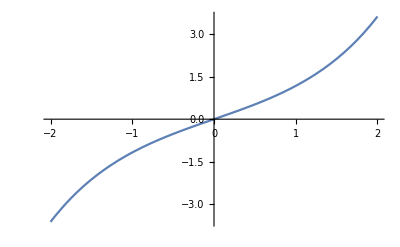

```mathematica
Plot[{Sinh[x]},{x,-2,2}]
```

```mathematica
f[x_]=c1 Sinh[β x]+c2 Cosh[β x]+c3 x Sinh[β x]+c4 x Cosh[β x];
```

```mathematica
φp[x_,y_]=(Y α)/β^2 qb Sin[β y];
φ[x_,y_]=f[x]Sin[β y]+φp[x,y];
```

```mathematica
φ[x,y]
```

Sin[y β] (c2 Cosh[x β]+c4 x Cosh[x β]+c1 Sinh[x β]+c3 x Sinh[x β])+(qb Y α Sinh[y β])/β^2

```mathematica
T11[x_,y_]=D[φ[x,y],{y,2}];
T12[x_,y_]=-D[D[φ[x,y],x],y];
T22[x_,y_]=D[φ[x,y],{x,2}];
```

```mathematica
FullSimplify[T11[x,y]/.{c1->0,c4->0}]
```

-Sin[y β] (qb Y α+β^2 (c2 Cosh[x β]+c3 x Sinh[x β]))

```mathematica
{c1s,c2s,c3s,c4s}={c1,c2,c3,c4}/.FullSimplify@First@Solve[{(Coefficient[T11[a,y],Sin[y β]])==0,(Coefficient[T11[-a,y],Sin[y β]])==0,(Coefficient[T12[a,y],Cos[y β] ])==0,(Coefficient[T12[-a,y],Cos[y β] ])==0},{c1,c2,c3,c4}]
```

{0,-(2 qb Y α (a β Cosh[a β]+Sinh[a β]))/(β^2 (2 a β+Sinh[2 a β])),(2 qb Y α Sinh[a β])/(β (2 a β+Sinh[2 a β])),0}

```mathematica
param
```

{Y→1,α→1,qb→1,β→1,a→1/2}

```mathematica
Sin[β x2]/.{β->Pi/(2 x2)}
```

1

```mathematica
T11s[x_,y_]=T11[x,y]/.{c1->c1s,c2->c2s,c3->c3s,c4->c4s}
```

-qb Y α Sin[y β]-β^2 Sin[y β] (-(2 qb Y α Cosh[x β] (a β Cosh[a β]+Sinh[a β]))/(β^2 (2 a β+Sinh[2 a β]))+(2 qb x Y α Sinh[a β] Sinh[x β])/(β (2 a β+Sinh[2 a β])))

```mathematica
T12s[x_,y_]=T12[x,y]/.{c1->c1s,c2->c2s,c3->c3s,c4->c4s}
```

-β Cos[y β] ((2 qb x Y α Cosh[x β] Sinh[a β])/(2 a β+Sinh[2 a β])+(2 qb Y α Sinh[a β] Sinh[x β])/(β (2 a β+Sinh[2 a β]))-(2 qb Y α (a β Cosh[a β]+Sinh[a β]) Sinh[x β])/(β (2 a β+Sinh[2 a β])))

```mathematica
T22s[x_,y_]=T22[x,y]/.{c1->c1s,c2->c2s,c3->c3s,c4->c4s}
```

Sin[y β] ((4 qb Y α Cosh[x β] Sinh[a β])/(2 a β+Sinh[2 a β])-(2 qb Y α Cosh[x β] (a β Cosh[a β]+Sinh[a β]))/(2 a β+Sinh[2 a β])+(2 qb x Y α β Sinh[a β] Sinh[x β])/(2 a β+Sinh[2 a β]))

```mathematica
FullSimplify@T12s[x,y]
```

(2 qb Y α β Cos[y β] (-x Cosh[x β] Sinh[a β]+a Cosh[a β] Sinh[x β]))/(2 a β+Sinh[2 a β])

```mathematica
param={Y->1,α->1,qb->10,β->2,a->1}
```

{Y→1,α→1,qb→10,β→2,a→1}

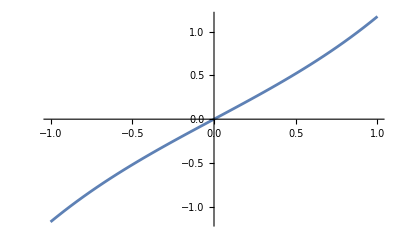

```mathematica
Plot[Sinh[x],{x,-1,1}]
```

```mathematica
Sin [β y]/.{y->Pi/(2β)}
```

1

```mathematica
FullSimplify@Solve[Sin [β y]==1,y]
```

{{y→ConditionalExpression[(π+4 π C[1])/(2 β), C[1]∈ℤ]}}

```mathematica
T22[x,y]
```

-qb Y α Sin[y β]-β^2 Sin[y β] (c2 Cosh[x β]+c4 x Cosh[x β]+c1 Sinh[x β]+c3 x Sinh[x β])

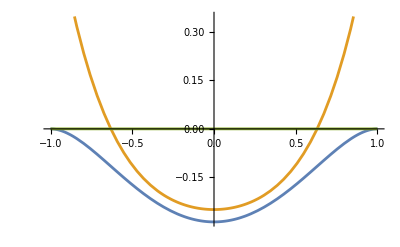

```mathematica
Plot[{(T11s[x,π/(2 β)]/(Y α qb))/.param,(T22s[x,π/(2 β)]/(Y α qb))/.param,(T12s[x,π/(2 β)]/(Y α qb))/.param},{x,-1,1}]
Plot[(T22s[x,π/(2 β)]/(Y α qb))/.param,{x,-1,1}]
Plot[(T12s[x,π/(2 β)]/(Y α qb))/.param,{x,-1,1}]
```

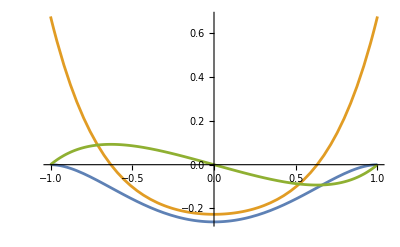

```mathematica
Plot[{(T11s[x,1]/(Y α qb))/.param,(T22s[x,1]/(Y α qb))/.param,(T12s[x,1]/(Y α qb))/.param},{x,-1,1}]
```

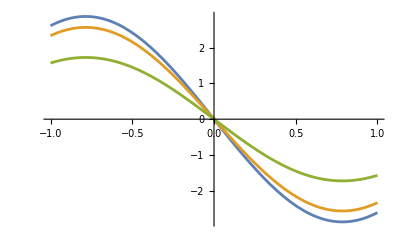

```mathematica
Plot[Evaluate[{T11s[0,y],T11s[1/4,y],T11s[1/2,y]}/.param],{y,-1,1}]
```

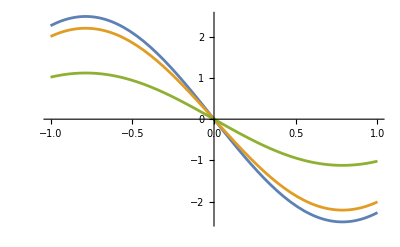

```mathematica
Plot[Evaluate[{T22s[0,y],T22s[1/4,y],T22s[1/2,y]}/.param],{y,-1,1}]
```

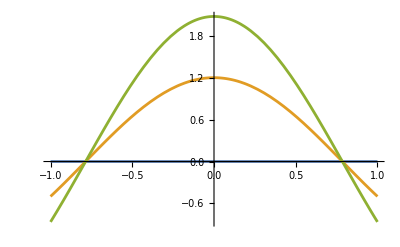

```mathematica
Plot[Evaluate[{T12s[0,y],T12s[1/4,y],T12s[1/2,y]}/.param],{y,-1,1}]
```

```mathematica
Plot3D[T11s[x,y]/.param,{x,-1,1},{y,-2,2}]
Plot3D[T11s[x,y]/.param,{x,-1,1},{y,-2,2}]
```

-Graphics3D-

-Graphics3D-

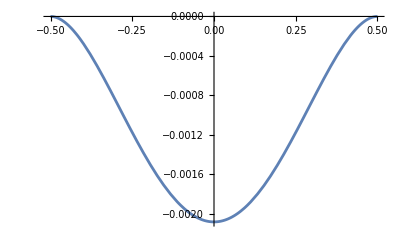

```mathematica
Plot[T11s[x,1]/.param,{x,-1/2,1/2}]
```

```mathematica
Plot3D[T12s[x,y]/.param,{x,-1/2,1/2},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[T22s[x,y]/.param,{x,-1/2,1/2},{y,-1,1}]
```

-Graphics3D-

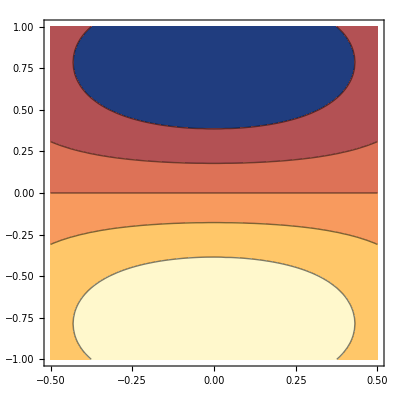

```mathematica
ContourPlot[T11s[x,y]/.param,{x,-1/2,1/2},{y,-1,1}]
```

```mathematica
E11[x_,y_]=1/Y((1+ν)T11s[x,y]-ν(T11s[x,y]+T22s[x,y]+α Sin[β y] ));
```

```mathematica
E22[x_,y_]=1/Y((1+ν)T22s[x,y]-ν(T11s[x,y]+T22s[x,y]+α Sin[β y] ));
E12[x_,y_]=1/Y((1+ν)T12s[x,y]);
```

```mathematica
Plot3D[E11[x,y]/.param/.{ν->1/3},{x,-1/2,1/2},{y,-1,1}]
```

-Graphics3D-

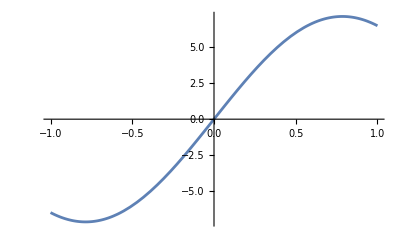

```mathematica
Plot[Evaluate[{E22[a,y]}/.param/.{ν->1/3}],{y,-1,1}]
```

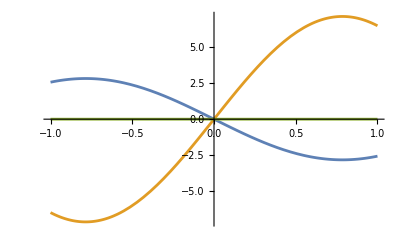

```mathematica
Plot[Evaluate[{E11[a,y],E22[a,y],E12[a,y]}/.param/.{ν->1/3}],{y,-1,1}]
```

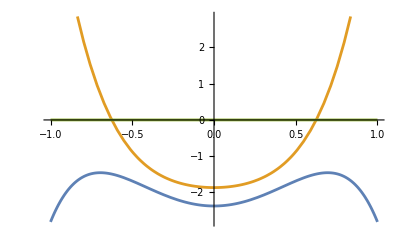

```mathematica
Plot[Evaluate[{E11[x,π/(2 β)],E22[x,π/(2 β)],E12[x,π/(2 β)]}/.param/.{ν->1/3}],{x,-1,1}]
```